```mathematica
cies={"AXP","BA","CAT","CSCO","CVX","DD","DIS","HD","IBM","INTC","JNJ","JPM","KO","MCD","MMM","MRK","MSFT","NKE","PFE","PG","TRV","UNH","UTX","V","VZ","WMT","XOM"};
```

```mathematica
properties={"Volume","Volatility20Day","Volatility50Day","Price"}
```

```mathematica
dates=First@Transpose[FinancialData["V","Price",{1990,01,01}]]
```

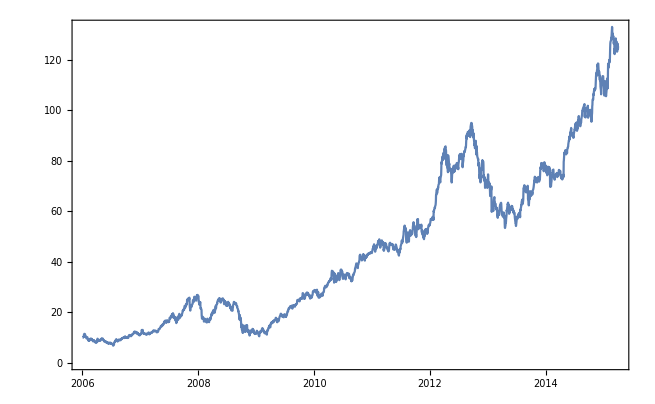

```mathematica
(*FinancialData["MSFT","Volatility50Day",{1990,01,01}];*)
DateListPlot[FinancialData["AAPL",{2006}]]
```

```mathematica
FinancialData["MSFT","Properties"]
```

{Ask,AskSize,Average200Day,Average50Day,AverageVolume3Month,Bid,BidSize,BookValuePerShare,Change,Change200Day,Change50Day,ChangeHigh52Week,ChangeLow52Week,CIK,Close,Company,CumulativeFractionalChange,CumulativeReturn,CUSIP,Dividend,DividendPerShare,DividendYield,EarningsPerShare,EBITDA,Exchange,FloatShares,ForwardEarnings,ForwardPERatio,FractionalChange,FractionalChange200Day,FractionalChange50Day,FractionalChangeHigh52Week,FractionalChangeLow52Week,High,High52Week,ISIN,LastTradeSize,LatestTrade,Lookup,Low,Low52Week,MarketCap,Name,OHLC,OHLCV,Open,PEGRatio,PERatio,Price,PriceTarget,PriceToBookRatio,PriceToSalesRatio,QuarterForwardEarnings,Range,Range52Week,RawClose,RawHigh,RawLow,RawOHLC,RawOpen,RawRange,Return,Sector,SEDOL,ShortRatio,SICCode,StandardName,Symbol,Volatility20Day,Volatility50Day,Volume,Website,YearEarningsEstimate,YearPERatioEstimate}

```mathematica
x["MSFT",1990]
```

{{2,1,0.44,0.328919,0.397584,53033600},{3,1,0.44,0.328919,0.393347,113772800},6360,{3,14,40.72,0.210229,0.308507,36752000},{4,14,40.29,0.204962,0.301985,37451600}}
 |  |  |  |

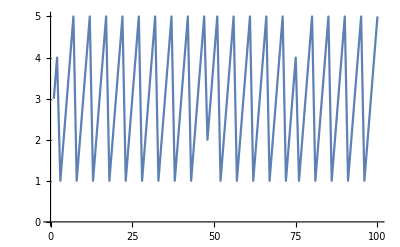

```mathematica
ListLinePlot[Take[dayNumber/@dates,100]]
```

```mathematica
Head[2.3]
```

Real

```mathematica
ClearAll[r]
```

```mathematica
ans=FinancialData["MSFT","Return",{1990}]
```

{{{1990,1,3},0.},{{1990,1,4},0.0227273},{{1990,1,5},-0.0222222},{{1990,1,8},0.0227273},{{1990,1,9},0.},6354,{{2015,3,30},-0.000244081},{{2015,3,31},-0.00732422},{{2015,4,1},0.00147565},{{2015,4,2},-0.0105599}}
 |  |  |  |

```mathematica
Last@Transpose@ans
```

{0.,0.0227273,-0.0222222,0.0227273,0.,-0.0222222,-0.0227273,0.,6347,0.000933271,-0.0335664,-0.00602991,-0.00582383,-0.000244081,-0.00732422,0.00147565,-0.0105599}
 |  |  |  |

```mathematica
FinancialData["MSFT","Price",{1990}]
```

{{{1990,1,2},0.44},{{1990,1,3},0.44},{{1990,1,4},0.45},{{1990,1,5},0.44},{{1990,1,8},0.45},{{1990,1,9},0.45},{{1990,1,10},0.44},{{1990,1,11},0.43},6349,{{2015,3,25},41.46},{{2015,3,26},41.21},{{2015,3,27},40.97},{{2015,3,30},40.96},{{2015,3,31},40.66},{{2015,4,1},40.72},{{2015,4,2},40.29}}
 |  |  |  |

```mathematica
Function[q,
With[{a=2},
q+2
]
][q]
```

2+q

```mathematica
ClearAll[x]
```

```mathematica
ans=x[2015]["MSFT"]
```

{{1,5,1,46.43,0.237129,0.197544,27913900},{1,1,2,46.,0.2301,0.196009,39673900},{1,2,2,45.33,0.230426,0.195036,36447900},{1,3,2,45.9,0.230108,0.19015,29114100},{1,4,2,47.25,0.236337,0.191929,29645200},{1,5,2,46.86,0.255228,0.200878,23942800},{1,1,3,46.27,0.256496,0.201811,23651900},{1,2,3,46.03,0.260165,0.201952,35270600},{1,3,3,45.64,0.259932,0.197438,29719600},{1,4,3,45.16,0.230701,0.196825,32742300},{1,5,3,45.91,0.229525,0.197978,35695300},{1,2,4,46.06,0.189,0.201269,36161900},{1,3,4,45.6,0.1891,0.19714,39081100},{1,4,4,46.8,0.188835,0.19823,35898000},{1,5,4,46.85,0.2112,0.20719,26211600},{1,1,5,46.68,0.210478,0.207225,42525500},{1,2,5,42.36,0.21005,0.207321,169164000},{1,3,5,40.9,0.408553,0.298085,84507100},{1,4,5,41.71,0.422401,0.306784,63585300},{1,5,5,40.11,0.432629,0.311285,78004900},{1,1,6,40.99,0.446797,0.321611,50352500},{1,2,6,41.31,0.459333,0.326327,52082400},{1,3,6,41.54,0.46072,0.3259,41614800},{1,4,6,42.15,0.457737,0.325331,36548200},{1,5,6,42.11,0.44549,0.327436,34311700},{1,1,7,42.06,0.445767,0.327451,31381100},{1,2,7,42.3,0.445187,0.32691,29670700},{1,3,7,42.08,0.446889,0.327327,38262500},{1,4,7,42.79,0.446631,0.32432,33268800},{1,5,7,43.56,0.452274,0.327327,40264900},{1,2,8,43.58,0.453116,0.330242,33695700},{1,3,8,43.53,0.452709,0.327817,27111700},{1,4,8,43.5,0.451907,0.327497,27603400},{1,5,8,43.86,0.43867,0.326108,29721100},{1,1,9,44.15,0.440569,0.326887,32518800},{1,2,9,44.09,0.442087,0.325989,25271700},{1,3,9,43.99,0.254059,0.325601,29759800},{1,4,9,44.06,0.211346,0.325511,28957300},{1,5,9,43.85,0.202517,0.325375,33807700},{1,1,10,43.88,0.127555,0.317054,31924000},{1,2,10,43.28,0.110085,0.31557,31748600},{1,3,10,43.06,0.125487,0.303845,25748700},{1,4,10,43.11,0.127775,0.303737,23193500},{1,5,10,42.36,0.118102,0.303164,36248800},{1,1,11,42.85,0.136366,0.303897,32108000},{1,2,11,42.03,0.142121,0.305424,39159700},{1,3,11,41.98,0.158735,0.307802,32215300},{1,4,11,41.02,0.157677,0.307438,59992500},{1,5,11,41.38,0.164694,0.310701,58007700},{1,1,12,41.56,0.152028,0.310933,35273500},{1,2,12,41.7,0.153805,0.310624,31673400},{1,3,12,42.5,0.15523,0.310444,44194800},{1,4,12,42.29,0.17351,0.312615,33679100},{1,5,12,42.88,0.170052,0.311068,71509000},{1,1,13,42.86,0.177055,0.305073,26049000},{1,2,13,42.9,0.177098,0.30474,25389500},{1,3,13,41.46,0.177284,0.303757,43136500},{1,4,13,41.21,0.213195,0.31255,37466500},{1,5,13,40.97,0.213377,0.312336,33820300},{1,1,14,40.96,0.213008,0.311845,34697100},{1,2,14,40.66,0.209648,0.308941,34802600},{1,3,14,40.72,0.210139,0.30887,36752000}}

```mathematica
x[2015]/@{"MSFT"}
```

{{{1,5,1,46.43,0.237129,0.197544,27913900},{1,1,2,46.,0.2301,0.196009,39673900},{1,2,2,45.33,0.230426,0.195036,36447900},{1,3,2,45.9,0.230108,0.19015,29114100},{1,4,2,47.25,0.236337,0.191929,29645200},{1,5,2,46.86,0.255228,0.200878,23942800},{1,1,3,46.27,0.256496,0.201811,23651900},{1,2,3,46.03,0.260165,0.201952,35270600},{1,3,3,45.64,0.259932,0.197438,29719600},{1,4,3,45.16,0.230701,0.196825,32742300},{1,5,3,45.91,0.229525,0.197978,35695300},{1,2,4,46.06,0.189,0.201269,36161900},{1,3,4,45.6,0.1891,0.19714,39081100},{1,4,4,46.8,0.188835,0.19823,35898000},{1,5,4,46.85,0.2112,0.20719,26211600},{1,1,5,46.68,0.210478,0.207225,42525500},{1,2,5,42.36,0.21005,0.207321,169164000},{1,3,5,40.9,0.408553,0.298085,84507100},{1,4,5,41.71,0.422401,0.306784,63585300},{1,5,5,40.11,0.432629,0.311285,78004900},{1,1,6,40.99,0.446797,0.321611,50352500},{1,2,6,41.31,0.459333,0.326327,52082400},{1,3,6,41.54,0.46072,0.3259,41614800},{1,4,6,42.15,0.457737,0.325331,36548200},{1,5,6,42.11,0.44549,0.327436,34311700},{1,1,7,42.06,0.445767,0.327451,31381100},{1,2,7,42.3,0.445187,0.32691,29670700},{1,3,7,42.08,0.446889,0.327327,38262500},{1,4,7,42.79,0.446631,0.32432,33268800},{1,5,7,43.56,0.452274,0.327327,40264900},{1,2,8,43.58,0.453116,0.330242,33695700},{1,3,8,43.53,0.452709,0.327817,27111700},{1,4,8,43.5,0.451907,0.327497,27603400},{1,5,8,43.86,0.43867,0.326108,29721100},{1,1,9,44.15,0.440569,0.326887,32518800},{1,2,9,44.09,0.442087,0.325989,25271700},{1,3,9,43.99,0.254059,0.325601,29759800},{1,4,9,44.06,0.211346,0.325511,28957300},{1,5,9,43.85,0.202517,0.325375,33807700},{1,1,10,43.88,0.127555,0.317054,31924000},{1,2,10,43.28,0.110085,0.31557,31748600},{1,3,10,43.06,0.125487,0.303845,25748700},{1,4,10,43.11,0.127775,0.303737,23193500},{1,5,10,42.36,0.118102,0.303164,36248800},{1,1,11,42.85,0.136366,0.303897,32108000},{1,2,11,42.03,0.142121,0.305424,39159700},{1,3,11,41.98,0.158735,0.307802,32215300},{1,4,11,41.02,0.157677,0.307438,59992500},{1,5,11,41.38,0.164694,0.310701,58007700},{1,1,12,41.56,0.152028,0.310933,35273500},{1,2,12,41.7,0.153805,0.310624,31673400},{1,3,12,42.5,0.15523,0.310444,44194800},{1,4,12,42.29,0.17351,0.312615,33679100},{1,5,12,42.88,0.170052,0.311068,71509000},{1,1,13,42.86,0.177055,0.305073,26049000},{1,2,13,42.9,0.177098,0.30474,25389500},{1,3,13,41.46,0.177284,0.303757,43136500},{1,4,13,41.21,0.213195,0.31255,37466500},{1,5,13,40.97,0.213377,0.312336,33820300},{1,1,14,40.96,0.213008,0.311845,34697100},{1,2,14,40.66,0.209648,0.308941,34802600},{1,3,14,40.72,0.210139,0.30887,36752000}}}

```mathematica
obj=objective[{"MSFT"},2015][q]
```

Min[-0.000133672+0.000133672 (1-q.{1,1,2,46.,0.2301,0.196009,39673900})-0.0145652 q.{1,1,2,46.,0.2301,0.196009,39673900},2 (-0.000133672+0.000133672 (1-q.{1,1,2,46.,0.2301,0.196009,39673900})-0.0145652 q.{1,1,2,46.,0.2301,0.196009,39673900})]+Min[-0.000133672+0.000133672 (1-q.{1,1,3,46.27,0.256496,0.201811,23651900})-0.00518695 q.{1,1,3,46.27,0.256496,0.201811,23651900},2 (-0.000133672+0.000133672 (1-q.{1,1,3,46.27,0.256496,0.201811,23651900})-0.00518695 q.{1,1,3,46.27,0.256496,0.201811,23651900})]+Min[-0.000133672+0.000133672 (1-q.{1,1,5,46.68,0.210478,0.207225,42525500})-0.092545 q.{1,1,5,46.68,0.210478,0.207225,42525500},2 (-0.000133672+0.000133672 (1-q.{1,1,5,46.68,0.210478,0.207225,42525500})-0.092545 q.{1,1,5,46.68,0.210478,0.207225,42525500})]+Min[-0.000133672+0.000133672 (1-q.{1,1,6,40.99,0.446797,0.321611,50352500})+0.00780678 q.{1,1,6,40.99,0.446797,0.321611,50352500},2 (-0.000133672+0.000133672 (1-q.{1,1,6,40.99,0.446797,0.321611,50352500})+0.00780678 q.{1,1,6,40.99,0.446797,0.321611,50352500})]+Min[-0.000133672+0.000133672 (1-q.{1,1,7,42.06,0.445767,0.327451,31381100})+0.00570613 q.{1,1,7,42.06,0.445767,0.327451,31381100},2 (-0.000133672+0.000133672 (1-q.{1,1,7,42.06,0.445767,0.327451,31381100})+0.00570613 q.{1,1,7,42.06,0.445767,0.327451,31381100})]+Min[-0.000133672+0.000133672 (1-q.{1,1,9,44.15,0.440569,0.326887,32518800})-0.001359 q.{1,1,9,44.15,0.440569,0.326887,32518800},2 (-0.000133672+0.000133672 (1-q.{1,1,9,44.15,0.440569,0.326887,32518800})-0.001359 q.{1,1,9,44.15,0.440569,0.326887,32518800})]+Min[-0.000133672+0.000133672 (1-q.{1,1,10,43.88,0.127555,0.317054,31924000})-0.0136737 q.{1,1,10,43.88,0.127555,0.317054,31924000},2 (-0.000133672+0.000133672 (1-q.{1,1,10,43.88,0.127555,0.317054,31924000})-0.0136737 q.{1,1,10,43.88,0.127555,0.317054,31924000})]+Min[-0.000133672+0.000133672 (1-q.{1,1,11,42.85,0.136366,0.303897,32108000})-0.0191365 q.{1,1,11,42.85,0.136366,0.303897,32108000},2 (-0.000133672+0.000133672 (1-q.{1,1,11,42.85,0.136366,0.303897,32108000})-0.0191365 q.{1,1,11,42.85,0.136366,0.303897,32108000})]+Min[-0.000133672+0.000133672 (1-q.{1,1,12,41.56,0.152028,0.310933,35273500})+0.00336862 q.{1,1,12,41.56,0.152028,0.310933,35273500},2 (-0.000133672+0.000133672 (1-q.{1,1,12,41.56,0.152028,0.310933,35273500})+0.00336862 q.{1,1,12,41.56,0.152028,0.310933,35273500})]+Min[-0.000133672+0.000133672 (1-q.{1,1,13,42.86,0.177055,0.305073,26049000})+0.000933271 q.{1,1,13,42.86,0.177055,0.305073,26049000},2 (-0.000133672+0.000133672 (1-q.{1,1,13,42.86,0.177055,0.305073,26049000})+0.000933271 q.{1,1,13,42.86,0.177055,0.305073,26049000})]+Min[-0.000133672+0.000133672 (1-q.{1,1,14,40.96,0.213008,0.311845,34697100})-0.00732422 q.{1,1,14,40.96,0.213008,0.311845,34697100},2 (-0.000133672+0.000133672 (1-q.{1,1,14,40.96,0.213008,0.311845,34697100})-0.00732422 q.{1,1,14,40.96,0.213008,0.311845,34697100})]+Min[-0.000133672+0.000133672 (1-q.{1,2,2,45.33,0.230426,0.195036,36447900})+0.0125745 q.{1,2,2,45.33,0.230426,0.195036,36447900},2 (-0.000133672+0.000133672 (1-q.{1,2,2,45.33,0.230426,0.195036,36447900})+0.0125745 q.{1,2,2,45.33,0.230426,0.195036,36447900})]+Min[-0.000133672+0.000133672 (1-q.{1,2,3,46.03,0.260165,0.201952,35270600})-0.00847274 q.{1,2,3,46.03,0.260165,0.201952,35270600},2 (-0.000133672+0.000133672 (1-q.{1,2,3,46.03,0.260165,0.201952,35270600})-0.00847274 q.{1,2,3,46.03,0.260165,0.201952,35270600})]+Min[-0.000133672+0.000133672 (1-q.{1,2,4,46.06,0.189,0.201269,36161900})-0.00998697 q.{1,2,4,46.06,0.189,0.201269,36161900},2 (-0.000133672+0.000133672 (1-q.{1,2,4,46.06,0.189,0.201269,36161900})-0.00998697 q.{1,2,4,46.06,0.189,0.201269,36161900})]+Min[-0.000133672+0.000133672 (1-q.{1,2,5,42.36,0.21005,0.207321,169164000})-0.0344665 q.{1,2,5,42.36,0.21005,0.207321,169164000},2 (-0.000133672+0.000133672 (1-q.{1,2,5,42.36,0.21005,0.207321,169164000})-0.0344665 q.{1,2,5,42.36,0.21005,0.207321,169164000})]+Min[-0.000133672+0.000133672 (1-q.{1,2,6,41.31,0.459333,0.326327,52082400})+0.00556766 q.{1,2,6,41.31,0.459333,0.326327,52082400},2 (-0.000133672+0.000133672 (1-q.{1,2,6,41.31,0.459333,0.326327,52082400})+0.00556766 q.{1,2,6,41.31,0.459333,0.326327,52082400})]+Min[-0.000133672+0.000133672 (1-q.{1,2,7,42.3,0.445187,0.32691,29670700})-0.00520095 q.{1,2,7,42.3,0.445187,0.32691,29670700},2 (-0.000133672+0.000133672 (1-q.{1,2,7,42.3,0.445187,0.32691,29670700})-0.00520095 q.{1,2,7,42.3,0.445187,0.32691,29670700})]+Min[-0.000133672+0.000133672 (1-q.{1,2,8,43.58,0.453116,0.330242,33695700})-0.00114732 q.{1,2,8,43.58,0.453116,0.330242,33695700},2 (-0.000133672+0.000133672 (1-q.{1,2,8,43.58,0.453116,0.330242,33695700})-0.00114732 q.{1,2,8,43.58,0.453116,0.330242,33695700})]+Min[-0.000133672+0.000133672 (1-q.{1,2,9,44.09,0.442087,0.325989,25271700})-0.00226809 q.{1,2,9,44.09,0.442087,0.325989,25271700},2 (-0.000133672+0.000133672 (1-q.{1,2,9,44.09,0.442087,0.325989,25271700})-0.00226809 q.{1,2,9,44.09,0.442087,0.325989,25271700})]+Min[-0.000133672+0.000133672 (1-q.{1,2,10,43.28,0.110085,0.31557,31748600})-0.00508318 q.{1,2,10,43.28,0.110085,0.31557,31748600},2 (-0.000133672+0.000133672 (1-q.{1,2,10,43.28,0.110085,0.31557,31748600})-0.00508318 q.{1,2,10,43.28,0.110085,0.31557,31748600})]+Min[-0.000133672+0.000133672 (1-q.{1,2,11,42.03,0.142121,0.305424,39159700})-0.00118963 q.{1,2,11,42.03,0.142121,0.305424,39159700},2 (-0.000133672+0.000133672 (1-q.{1,2,11,42.03,0.142121,0.305424,39159700})-0.00118963 q.{1,2,11,42.03,0.142121,0.305424,39159700})]+Min[-0.000133672+0.000133672 (1-q.{1,2,12,41.7,0.153805,0.310624,31673400})+0.0191847 q.{1,2,12,41.7,0.153805,0.310624,31673400},2 (-0.000133672+0.000133672 (1-q.{1,2,12,41.7,0.153805,0.310624,31673400})+0.0191847 q.{1,2,12,41.7,0.153805,0.310624,31673400})]+Min[-0.000133672+0.000133672 (1-q.{1,2,13,42.9,0.177098,0.30474,25389500})-0.0335664 q.{1,2,13,42.9,0.177098,0.30474,25389500},2 (-0.000133672+0.000133672 (1-q.{1,2,13,42.9,0.177098,0.30474,25389500})-0.0335664 q.{1,2,13,42.9,0.177098,0.30474,25389500})]+Min[-0.000133672+0.000133672 (1-q.{1,2,14,40.66,0.209648,0.308941,34802600})+0.00147565 q.{1,2,14,40.66,0.209648,0.308941,34802600},2 (-0.000133672+0.000133672 (1-q.{1,2,14,40.66,0.209648,0.308941,34802600})+0.00147565 q.{1,2,14,40.66,0.209648,0.308941,34802600})]+Min[-0.000133672+0.000133672 (1-q.{1,3,2,45.9,0.230108,0.19015,29114100})+0.0294118 q.{1,3,2,45.9,0.230108,0.19015,29114100},2 (-0.000133672+0.000133672 (1-q.{1,3,2,45.9,0.230108,0.19015,29114100})+0.0294118 q.{1,3,2,45.9,0.230108,0.19015,29114100})]+Min[-0.000133672+0.000133672 (1-q.{1,3,3,45.64,0.259932,0.197438,29719600})-0.0105171 q.{1,3,3,45.64,0.259932,0.197438,29719600},2 (-0.000133672+0.000133672 (1-q.{1,3,3,45.64,0.259932,0.197438,29719600})-0.0105171 q.{1,3,3,45.64,0.259932,0.197438,29719600})]+Min[-0.000133672+0.000133672 (1-q.{1,3,4,45.6,0.1891,0.19714,39081100})+0.0263158 q.{1,3,4,45.6,0.1891,0.19714,39081100},2 (-0.000133672+0.000133672 (1-q.{1,3,4,45.6,0.1891,0.19714,39081100})+0.0263158 q.{1,3,4,45.6,0.1891,0.19714,39081100})]+Min[-0.000133672+0.000133672 (1-q.{1,3,5,40.9,0.408553,0.298085,84507100})+0.0198044 q.{1,3,5,40.9,0.408553,0.298085,84507100},2 (-0.000133672+0.000133672 (1-q.{1,3,5,40.9,0.408553,0.298085,84507100})+0.0198044 q.{1,3,5,40.9,0.408553,0.298085,84507100})]+Min[-0.000133672+0.000133672 (1-q.{1,3,6,41.54,0.46072,0.3259,41614800})+0.0146846 q.{1,3,6,41.54,0.46072,0.3259,41614800},2 (-0.000133672+0.000133672 (1-q.{1,3,6,41.54,0.46072,0.3259,41614800})+0.0146846 q.{1,3,6,41.54,0.46072,0.3259,41614800})]+Min[-0.000133672+0.000133672 (1-q.{1,3,7,42.08,0.446889,0.327327,38262500})+0.0168726 q.{1,3,7,42.08,0.446889,0.327327,38262500},2 (-0.000133672+0.000133672 (1-q.{1,3,7,42.08,0.446889,0.327327,38262500})+0.0168726 q.{1,3,7,42.08,0.446889,0.327327,38262500})]+Min[-0.000133672+0.000133672 (1-q.{1,3,8,43.53,0.452709,0.327817,27111700})-0.00068918 q.{1,3,8,43.53,0.452709,0.327817,27111700},2 (-0.000133672+0.000133672 (1-q.{1,3,8,43.53,0.452709,0.327817,27111700})-0.00068918 q.{1,3,8,43.53,0.452709,0.327817,27111700})]+Min[-0.000133672+0.000133672 (1-q.{1,3,9,43.99,0.254059,0.325601,29759800})+0.00159127 q.{1,3,9,43.99,0.254059,0.325601,29759800},2 (-0.000133672+0.000133672 (1-q.{1,3,9,43.99,0.254059,0.325601,29759800})+0.00159127 q.{1,3,9,43.99,0.254059,0.325601,29759800})]+Min[-0.000133672+0.000133672 (1-q.{1,3,10,43.06,0.125487,0.303845,25748700})+0.00116117 q.{1,3,10,43.06,0.125487,0.303845,25748700},2 (-0.000133672+0.000133672 (1-q.{1,3,10,43.06,0.125487,0.303845,25748700})+0.00116117 q.{1,3,10,43.06,0.125487,0.303845,25748700})]+Min[-0.000133672+0.000133672 (1-q.{1,3,11,41.98,0.158735,0.307802,32215300})-0.022868 q.{1,3,11,41.98,0.158735,0.307802,32215300},2 (-0.000133672+0.000133672 (1-q.{1,3,11,41.98,0.158735,0.307802,32215300})-0.022868 q.{1,3,11,41.98,0.158735,0.307802,32215300})]+Min[-0.000133672+0.000133672 (1-q.{1,3,12,42.5,0.15523,0.310444,44194800})-0.00494118 q.{1,3,12,42.5,0.15523,0.310444,44194800},2 (-0.000133672+0.000133672 (1-q.{1,3,12,42.5,0.15523,0.310444,44194800})-0.00494118 q.{1,3,12,42.5,0.15523,0.310444,44194800})]+Min[-0.000133672+0.000133672 (1-q.{1,3,13,41.46,0.177284,0.303757,43136500})-0.00602991 q.{1,3,13,41.46,0.177284,0.303757,43136500},2 (-0.000133672+0.000133672 (1-q.{1,3,13,41.46,0.177284,0.303757,43136500})-0.00602991 q.{1,3,13,41.46,0.177284,0.303757,43136500})]+Min[-0.000133672+0.000133672 (1-q.{1,3,14,40.72,0.210139,0.30887,36752000})-0.0105599 q.{1,3,14,40.72,0.210139,0.30887,36752000},2 (-0.000133672+0.000133672 (1-q.{1,3,14,40.72,0.210139,0.30887,36752000})-0.0105599 q.{1,3,14,40.72,0.210139,0.30887,36752000})]+Min[-0.000133672+0.000133672 (1-q.{1,4,2,47.25,0.236337,0.191929,29645200})-0.00825397 q.{1,4,2,47.25,0.236337,0.191929,29645200},2 (-0.000133672+0.000133672 (1-q.{1,4,2,47.25,0.236337,0.191929,29645200})-0.00825397 q.{1,4,2,47.25,0.236337,0.191929,29645200})]+Min[-0.000133672+0.000133672 (1-q.{1,4,3,45.16,0.230701,0.196825,32742300})+0.0166076 q.{1,4,3,45.16,0.230701,0.196825,32742300},2 (-0.000133672+0.000133672 (1-q.{1,4,3,45.16,0.230701,0.196825,32742300})+0.0166076 q.{1,4,3,45.16,0.230701,0.196825,32742300})]+Min[-0.000133672+0.000133672 (1-q.{1,4,4,46.8,0.188835,0.19823,35898000})+0.00106838 q.{1,4,4,46.8,0.188835,0.19823,35898000},2 (-0.000133672+0.000133672 (1-q.{1,4,4,46.8,0.188835,0.19823,35898000})+0.00106838 q.{1,4,4,46.8,0.188835,0.19823,35898000})]+Min[-0.000133672+0.000133672 (1-q.{1,4,5,41.71,0.422401,0.306784,63585300})-0.0383601 q.{1,4,5,41.71,0.422401,0.306784,63585300},2 (-0.000133672+0.000133672 (1-q.{1,4,5,41.71,0.422401,0.306784,63585300})-0.0383601 q.{1,4,5,41.71,0.422401,0.306784,63585300})]+Min[-0.000133672+0.000133672 (1-q.{1,4,6,42.15,0.457737,0.325331,36548200})-0.000948992 q.{1,4,6,42.15,0.457737,0.325331,36548200},2 (-0.000133672+0.000133672 (1-q.{1,4,6,42.15,0.457737,0.325331,36548200})-0.000948992 q.{1,4,6,42.15,0.457737,0.325331,36548200})]+Min[-0.000133672+0.000133672 (1-q.{1,4,7,42.79,0.446631,0.32432,33268800})+0.0179949 q.{1,4,7,42.79,0.446631,0.32432,33268800},2 (-0.000133672+0.000133672 (1-q.{1,4,7,42.79,0.446631,0.32432,33268800})+0.0179949 q.{1,4,7,42.79,0.446631,0.32432,33268800})]+Min[-0.000133672+0.000133672 (1-q.{1,4,8,43.5,0.451907,0.327497,27603400})+0.00827586 q.{1,4,8,43.5,0.451907,0.327497,27603400},2 (-0.000133672+0.000133672 (1-q.{1,4,8,43.5,0.451907,0.327497,27603400})+0.00827586 q.{1,4,8,43.5,0.451907,0.327497,27603400})]+Min[-0.000133672+0.000133672 (1-q.{1,4,9,44.06,0.211346,0.325511,28957300})-0.00476623 q.{1,4,9,44.06,0.211346,0.325511,28957300},2 (-0.000133672+0.000133672 (1-q.{1,4,9,44.06,0.211346,0.325511,28957300})-0.00476623 q.{1,4,9,44.06,0.211346,0.325511,28957300})]+Min[-0.000133672+0.000133672 (1-q.{1,4,10,43.11,0.127775,0.303737,23193500})-0.0173974 q.{1,4,10,43.11,0.127775,0.303737,23193500},2 (-0.000133672+0.000133672 (1-q.{1,4,10,43.11,0.127775,0.303737,23193500})-0.0173974 q.{1,4,10,43.11,0.127775,0.303737,23193500})]+Min[-0.000133672+0.000133672 (1-q.{1,4,11,41.02,0.157677,0.307438,59992500})+0.00877621 q.{1,4,11,41.02,0.157677,0.307438,59992500},2 (-0.000133672+0.000133672 (1-q.{1,4,11,41.02,0.157677,0.307438,59992500})+0.00877621 q.{1,4,11,41.02,0.157677,0.307438,59992500})]+Min[-0.000133672+0.000133672 (1-q.{1,4,12,42.29,0.17351,0.312615,33679100})+0.0139513 q.{1,4,12,42.29,0.17351,0.312615,33679100},2 (-0.000133672+0.000133672 (1-q.{1,4,12,42.29,0.17351,0.312615,33679100})+0.0139513 q.{1,4,12,42.29,0.17351,0.312615,33679100})]+Min[-0.000133672+0.000133672 (1-q.{1,4,13,41.21,0.213195,0.31255,37466500})-0.00582383 q.{1,4,13,41.21,0.213195,0.31255,37466500},2 (-0.000133672+0.000133672 (1-q.{1,4,13,41.21,0.213195,0.31255,37466500})-0.00582383 q.{1,4,13,41.21,0.213195,0.31255,37466500})]+Min[-0.000133672+0.000133672 (1-q.{1,4,14,40.29,0.210229,0.308507,37451600})+0.0312733 q.{1,4,14,40.29,0.210229,0.308507,37451600},2 (-0.000133672+0.000133672 (1-q.{1,4,14,40.29,0.210229,0.308507,37451600})+0.0312733 q.{1,4,14,40.29,0.210229,0.308507,37451600})]+Min[-0.000133672+0.000133672 (1-q.{1,5,1,46.43,0.237129,0.197544,27913900})-0.00926125 q.{1,5,1,46.43,0.237129,0.197544,27913900},2 (-0.000133672+0.000133672 (1-q.{1,5,1,46.43,0.237129,0.197544,27913900})-0.00926125 q.{1,5,1,46.43,0.237129,0.197544,27913900})]+Min[-0.000133672+0.000133672 (1-q.{1,5,2,46.86,0.255228,0.200878,23942800})-0.0125907 q.{1,5,2,46.86,0.255228,0.200878,23942800},2 (-0.000133672+0.000133672 (1-q.{1,5,2,46.86,0.255228,0.200878,23942800})-0.0125907 q.{1,5,2,46.86,0.255228,0.200878,23942800})]+Min[-0.000133672+0.000133672 (1-q.{1,5,3,45.91,0.229525,0.197978,35695300})+0.00326726 q.{1,5,3,45.91,0.229525,0.197978,35695300},2 (-0.000133672+0.000133672 (1-q.{1,5,3,45.91,0.229525,0.197978,35695300})+0.00326726 q.{1,5,3,45.91,0.229525,0.197978,35695300})]+Min[-0.000133672+0.000133672 (1-q.{1,5,4,46.85,0.2112,0.20719,26211600})-0.0036286 q.{1,5,4,46.85,0.2112,0.20719,26211600},2 (-0.000133672+0.000133672 (1-q.{1,5,4,46.85,0.2112,0.20719,26211600})-0.0036286 q.{1,5,4,46.85,0.2112,0.20719,26211600})]+Min[-0.000133672+0.000133672 (1-q.{1,5,5,40.11,0.432629,0.311285,78004900})+0.0219397 q.{1,5,5,40.11,0.432629,0.311285,78004900},2 (-0.000133672+0.000133672 (1-q.{1,5,5,40.11,0.432629,0.311285,78004900})+0.0219397 q.{1,5,5,40.11,0.432629,0.311285,78004900})]+Min[-0.000133672+0.000133672 (1-q.{1,5,6,42.11,0.44549,0.327436,34311700})-0.00118737 q.{1,5,6,42.11,0.44549,0.327436,34311700},2 (-0.000133672+0.000133672 (1-q.{1,5,6,42.11,0.44549,0.327436,34311700})-0.00118737 q.{1,5,6,42.11,0.44549,0.327436,34311700})]+Min[-0.000133672+0.000133672 (1-q.{1,5,7,43.56,0.452274,0.327327,40264900})+0.00757576 q.{1,5,7,43.56,0.452274,0.327327,40264900},2 (-0.000133672+0.000133672 (1-q.{1,5,7,43.56,0.452274,0.327327,40264900})+0.00757576 q.{1,5,7,43.56,0.452274,0.327327,40264900})]+Min[-0.000133672+0.000133672 (1-q.{1,5,8,43.86,0.43867,0.326108,29721100})+0.00661195 q.{1,5,8,43.86,0.43867,0.326108,29721100},2 (-0.000133672+0.000133672 (1-q.{1,5,8,43.86,0.43867,0.326108,29721100})+0.00661195 q.{1,5,8,43.86,0.43867,0.326108,29721100})]+Min[-0.000133672+0.000133672 (1-q.{1,5,9,43.85,0.202517,0.325375,33807700})+0.000684151 q.{1,5,9,43.85,0.202517,0.325375,33807700},2 (-0.000133672+0.000133672 (1-q.{1,5,9,43.85,0.202517,0.325375,33807700})+0.000684151 q.{1,5,9,43.85,0.202517,0.325375,33807700})]+Min[-0.000133672+0.000133672 (1-q.{1,5,10,42.36,0.118102,0.303164,36248800})+0.0115675 q.{1,5,10,42.36,0.118102,0.303164,36248800},2 (-0.000133672+0.000133672 (1-q.{1,5,10,42.36,0.118102,0.303164,36248800})+0.0115675 q.{1,5,10,42.36,0.118102,0.303164,36248800})]+Min[-0.000133672+0.000133672 (1-q.{1,5,11,41.38,0.164694,0.310701,58007700})+0.00434993 q.{1,5,11,41.38,0.164694,0.310701,58007700},2 (-0.000133672+0.000133672 (1-q.{1,5,11,41.38,0.164694,0.310701,58007700})+0.00434993 q.{1,5,11,41.38,0.164694,0.310701,58007700})]+Min[-0.000133672+0.000133672 (1-q.{1,5,12,42.88,0.170052,0.311068,71509000})-0.000466418 q.{1,5,12,42.88,0.170052,0.311068,71509000},2 (-0.000133672+0.000133672 (1-q.{1,5,12,42.88,0.170052,0.311068,71509000})-0.000466418 q.{1,5,12,42.88,0.170052,0.311068,71509000})]+Min[-0.000133672+0.000133672 (1-q.{1,5,13,40.97,0.213377,0.312336,33820300})-0.000244081 q.{1,5,13,40.97,0.213377,0.312336,33820300},2 (-0.000133672+0.000133672 (1-q.{1,5,13,40.97,0.213377,0.312336,33820300})-0.000244081 q.{1,5,13,40.97,0.213377,0.312336,33820300})]

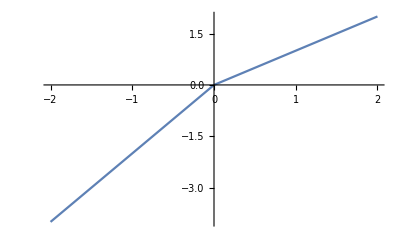

```mathematica
Plot[U[x],{x,-2,2}]
```

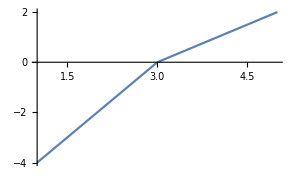
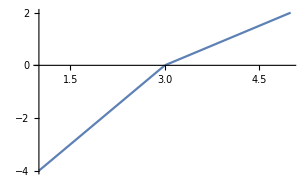

```mathematica
{Plot[Min[2(x-3),x-3],{x,1,5}],Plot[Max[x-3,0]-2Max[3-x,0],{x,1,5}]}
```

```mathematica
LinearProgramming
```

```mathematica
{Array[m,{3,3}]//MatrixForm,
Array[g,{3,3}]//MatrixForm}
Array[m,{3,3}].Array[g,{3,3}]//MatrixForm
```

{(m[1,1] | m[1,2] | m[1,3]
m[2,1] | m[2,2] | m[2,3]
m[3,1] | m[3,2] | m[3,3]),(g[1,1] | g[1,2] | g[1,3]
g[2,1] | g[2,2] | g[2,3]
g[3,1] | g[3,2] | g[3,3])}

(g[1,1] m[1,1]+g[2,1] m[1,2]+g[3,1] m[1,3] | g[1,2] m[1,1]+g[2,2] m[1,2]+g[3,2] m[1,3] | g[1,3] m[1,1]+g[2,3] m[1,2]+g[3,3] m[1,3]
g[1,1] m[2,1]+g[2,1] m[2,2]+g[3,1] m[2,3] | g[1,2] m[2,1]+g[2,2] m[2,2]+g[3,2] m[2,3] | g[1,3] m[2,1]+g[2,3] m[2,2]+g[3,3] m[2,3]
g[1,1] m[3,1]+g[2,1] m[3,2]+g[3,1] m[3,3] | g[1,2] m[3,1]+g[2,2] m[3,2]+g[3,2] m[3,3] | g[1,3] m[3,1]+g[2,3] m[3,2]+g[3,3] m[3,3])

```mathematica
l=7;
```

```mathematica
SparseArray[ArrayFlatten@{{IdentityMatrix[l],IdentityMatrix[l]}}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
SparseArray[ArrayFlatten@{{IdentityMatrix[l],IdentityMatrix[l]}}]
```

SparseArray[<14>, {7, 14}]

```mathematica
my=Array[m,{3,3}]
```

{{m[1,1],m[1,2],m[1,3]},{m[2,1],m[2,2],m[2,3]},{m[3,1],m[3,2],m[3,3]}}

```mathematica
my*{a,b,c}//MatrixForm
```

(a m[1,1] | a m[1,2] | a m[1,3]
b m[2,1] | b m[2,2] | b m[2,3]
c m[3,1] | c m[3,2] | c m[3,3])

```mathematica
Transpose[Transpose@my*{a,b,c}]//MatrixForm
```

(a m[1,1] | b m[1,2] | c m[1,3]
a m[2,1] | b m[2,2] | c m[2,3]
a m[3,1] | b m[3,2] | c m[3,3])

```mathematica
stocks={"MSFT"};
y=2015;
```

```mathematica
solveObjective[{"MSFT"},2015]
```

LinearProgramming::lpdim: Invalid input: the dimensions of the input vectors or matrices must match.

{{137},{65,137},{137}}